```mathematica
Clear@Evaluate[Context[]<>"*"]
SetDirectory@NotebookDirectory[];
```

```mathematica
<<"Definitions/IO.wl"
```

```mathematica
RawDataBCP=Import@GetZFileBCP[-1,1,1];
ZBCP=DeleteCases[#,{ω_,Z_}/;ω>0.55]&/@GroupBy[{#1,#2 (1+√(1-#1^2)),#3}&@@@MapAt[N@Round[#,10^-3]&,RawDataBCP,{All,1}],First->(Drop[#,1]&)];
```

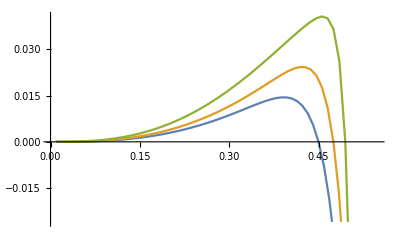

```mathematica
ListPlot[ZBCP/@{0.9,0.95,0.99},Joined->True]
```